```mathematica
alpha = 1;
beta = 10;
fact[x_,n_]:=(alpha + beta*x^n/(1+x^n))/(alpha+beta);
frep[x_,n_]:=(alpha + beta*1/(1+x^n))/(alpha+beta);
```

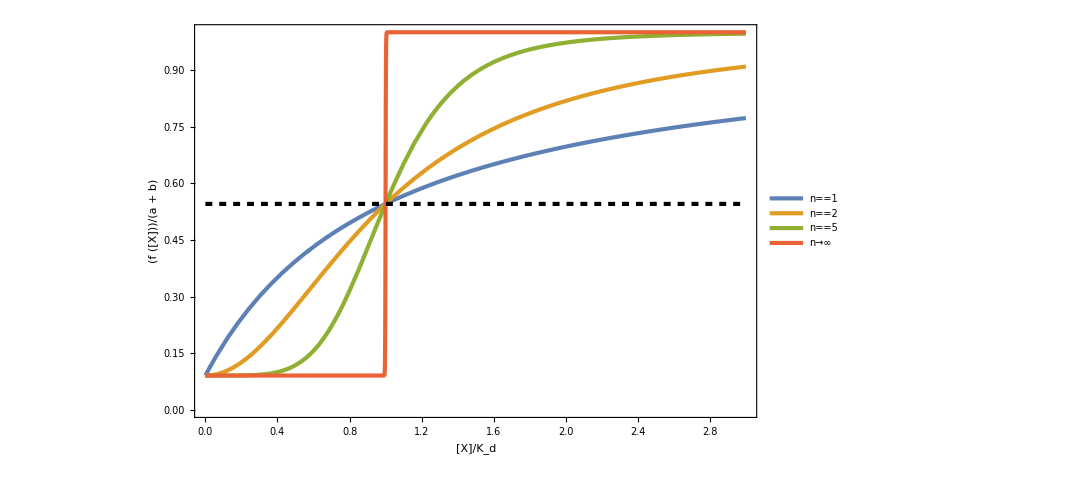

```mathematica
optGen = {Frame->True,FrameStyle->Directive[Black,Thick],RotateLabel->False,LabelStyle->Directive[35,FontFamily->"Palatino Linotype",Black]}; 
imSize = {ImageSize->800};
optLab=FrameLabel->{"[X]/K_d","(f ([X]))/(a + b)"};
optStyle = PlotStyle->{{ColorData[97,"ColorList"][[1]],AbsoluteThickness[3]},{ColorData[97,"ColorList"][[2]],AbsoluteThickness[3]},{ColorData[97,"ColorList"][[3]],AbsoluteThickness[3]},{ColorData[97,"ColorList"][[4]],AbsoluteThickness[3]},{Black,Dashed,AbsoluteThickness[3]}};
legendAct={PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["n=1",TeXForm,HoldForm]]],Text[Style[ToExpression["n=2",TeXForm,HoldForm]]],Text[Style[ToExpression["n=5",TeXForm,HoldForm]]],Text[Style[ToExpression["n\\to\\infty",TeXForm,HoldForm]]]},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",25},LegendLayout->{"Row",4},Spacings->0.1],{0.85,0.25}]};

Show[Plot[{fact[x,1],fact[x,2],fact[x,5], fact[x,1000], (alpha+0.5*beta)/(alpha+beta)},{x,0,3},Evaluate[optGen],Evaluate[optStyle],Evaluate[optLab],Evaluate[legendAct]],Evaluate[imSize]]
```

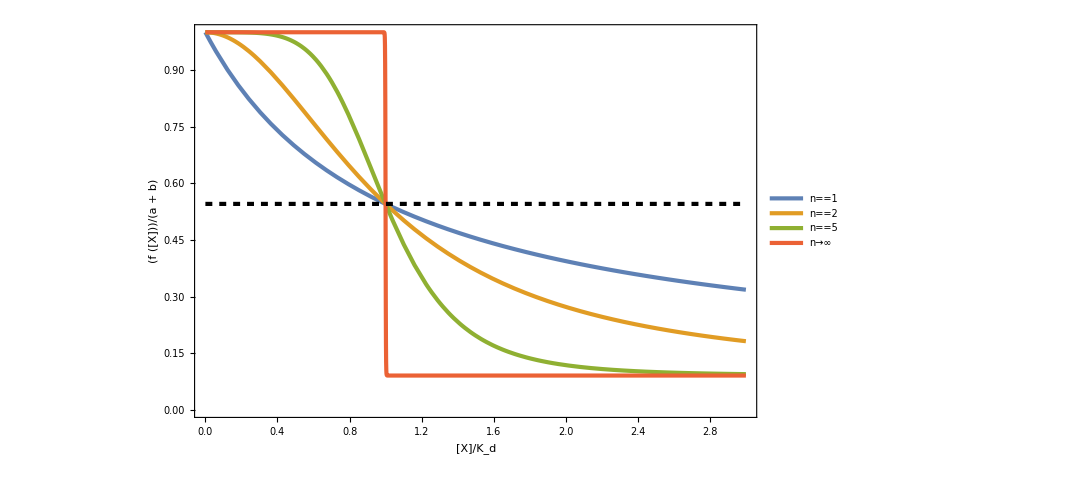

```mathematica
legendRep={PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["n=1",TeXForm,HoldForm]]],Text[Style[ToExpression["n=2",TeXForm,HoldForm]]],Text[Style[ToExpression["n=5",TeXForm,HoldForm]]],Text[Style[ToExpression["n\\to\\infty",TeXForm,HoldForm]]]},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",25},LegendLayout->{"Row",4},Spacings->0.1],{0.85,0.77}]};
Show[Plot[{frep[x,1],frep[x,2],frep[x,5], frep[x,1000], (alpha+0.5*beta)/(alpha+beta)},{x,0,3},Evaluate[optGen],Evaluate[optStyle],Evaluate[optLab],Evaluate[legendRep]],Evaluate[imSize]]
```